```mathematica
Quit[]
```

## Load Model and Compute Diagrams

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
$FCVerbose=1;
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-SMQCD-NLO_FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
```

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →3, with {} →{-F[9],F[9],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3}).
However the choice below produces nicer diagrams.

generic model {Lorentz} initialized

classes model {../../FA_models/SMS-stop-SMQCD-NLO_FA} initialized

in total: 6 Particles insertions

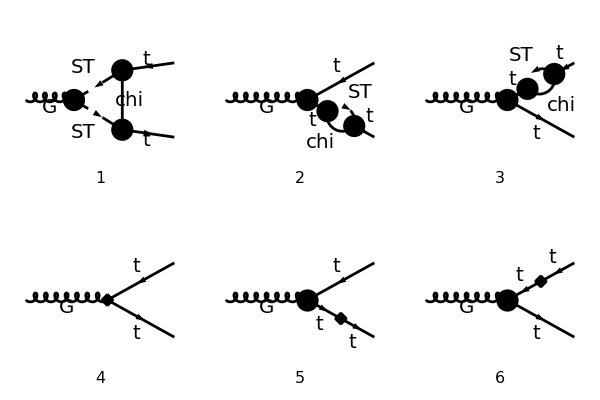

```mathematica
topsCT = CreateCTTopologies[1,1->2];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
processGGT =  {V[1]}->  {-F[3],F[3]};
allDiags = InsertFields[Join[tops,topsCT],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[2],V[3]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{3,2},ImageSize->{ 600,400},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

## Compute Amplitude

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3},OutgoingMomenta->{-p1,-p2},LoopMomenta->{q},List->False,SUNIndexNames->{cc3,aa,bb},SUNFIndexNames->{a,c1,c2},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,FR$deltaZ[{G,G},{{}}]->deltaZG,FR$deltaZ[{t,t},{{}},"L"]->deltaZL,FR$deltaZ[{t,t},{{}},"R"]->deltaZR,FR$delta[{MT},{}]->deltaM,FR$delta[{aS},{}]->deltaaS};
ampB =FullSimplify[SUNSimplify[DiracSimplify[FCReplaceMomenta[ampA,{p3->-p1-p2}]]]];
```

in total: 6 Particles amplitudes

Simplify counter-terms (see top_SelfEnergy_CT.nb and top-Vertex_CT.nb):

```mathematica
CTsubs={deltaZG->0,deltaaS->0,deltaZL -> Pi^2yDM^2  MT^2  Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]],deltaZR-> Pi^2  yDM^2( MT^2 Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]]+Re[B1[MT^2,mChi^2,mST^2,BReduce->False]]),deltaM->-Pi^2/2 yDM^2 MT Re[B1[MT^2,mChi^2,mST^2,BReduce->False]]};
ampB2=ampB/.CTsubs;
```

Evaluate Loop integrals:

```mathematica
ampC =FCCanonicalizeDummyIndices[( TID[ampB2,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify),LorentzIndexNames-> {μ,ν}];
```

```mathematica
FCClearScalarProducts[];
SPD[p1,p2]=1/2(s-SPD[p1,p1]-SPD[p2,p2]);
ampD=FullSimplify[DiracSimplify[FCReplaceMomenta[ampC,{p3->-p1-p2}]]];
ampEsimp2=Simplify[(ExpandScalarProduct[DiracSimplify[ampD]])];
```

## Check Divergences (note that the DB1 loop integral is finite)

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,B1,DB1,PaVe}];
lIntsUV=Table[lInt->PaXEvaluateUV[lInt,PaXImplicitPrefactor->1/(2 Pi)^4],{lInt,lInts}];
lIntsUV//MatrixForm
```

PaXEvaluate::convFail: Warning! Not all scalar loop integrals in the expression could be prepared to be processed with Package X. Following integrals will not be handled by Package X: {DB1(MT^2,mChi^2,mST^2,BReduce→False)}

(B_1(MT^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
DB1(MT^2,mChi^2,mST^2,BReduce→False)→0
B_1(p1^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
B_1(p2^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
C_1(p1^2,s,p2^2,mChi^2,mST^2,mST^2)→0
C_2(p1^2,s,p2^2,mChi^2,mST^2,mST^2)→0
C_00(p1^2,s,p2^2,mChi^2,mST^2,mST^2)→1/(64 π^4 ε_UV)
C_11(p1^2,s,p2^2,mChi^2,mST^2,mST^2)→0
C_12(p1^2,s,p2^2,mChi^2,mST^2,mST^2)→0
C_22(p1^2,s,p2^2,mChi^2,mST^2,mST^2)→0)

```mathematica
loopUV=FullSimplify[ampEsimp2/.lIntsUV,Assumptions->{EpsilonUV ∈Reals}]
```

0

## Simplify Result

### Replace momenta squared

```mathematica
ampEsimp3a=Simplify[DiracSimplify[FeynAmpDenominatorExplicit[ampEsimp2]]/.{Pair[Momentum[p1,D],Momentum[p1,D]]->p1sq,Pair[Momentum[p2,D],Momentum[p2,D]]->p2sq}];
```

### Order PaVe integrals (note that B1 and DB1 are already ordered as B1[x] = B1[x,mChi^2,mST^2] and DB1[x] = DB1[x,mChi^2,mST^2])

```mathematica
lInts = Cases2[ampEsimp3a,{A0,B0,C0,B1,D0,PaVe}];
orderedPaVes=Table[lInt->PaVeOrder[lInt,PaVeOrderList->{s,p2sq,mChi^2,mST^2,mST^2},Sum->True],{lInt,lInts}];
ampEsimp4=ampEsimp3a/.orderedPaVes;
lIntsOrdered = Cases2[ampEsimp4,{A0,B0,C0,D0,B1,DB1,PaVe}];
lIntsOrdered//MatrixForm
```

(B_1(MT^2,mChi^2,mST^2)
DB1(MT^2,mChi^2,mST^2,BReduce→False)
B_1(p1sq,mChi^2,mST^2)
B_1(p2sq,mChi^2,mST^2)
C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_2(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_00(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_12(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_22(p1sq,s,p2sq,mChi^2,mST^2,mST^2))

### Simplify arguments of PaVe integrals

```mathematica
massArgs={mChi^2,mST^2,mST^2};
subsPaVe={
B1[a1_,mChi^2,mST^2,__]:>B1[a1],
PaVe[1,{a1_},{mChi^2,mST^2},__]:>B1[a1],
DB1[a1_,mChi^2,mST^2,__]:>DB1[a1],
PaVe[0,0,{a1_,a2_,a3_},massArgs,__]:>C00[a1,a2,a3],
PaVe[1,1,{a1_,a2_,a3_},massArgs,__]:>C11[a1,a2,a3],
PaVe[2,2,{a1_,a2_,a3_},massArgs,__]:>C22[a1,a2,a3],
PaVe[1,2,{a1_,a2_,a3_},massArgs,__]:>C12[a1,a2,a3],
PaVe[1,{a1_,a2_,a3_},massArgs,__]:>C1[a1,a2,a3],
PaVe[2,{a1_,a2_,a3_},massArgs,__]:>C2[a1,a2,a3]};
```

```mathematica
ampEsimp5=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp4]]/.subsPaVe;
```

## Extract Tensor Structure

First group terms by number of gamma matrices and momenta

```mathematica
spinorChains=DeleteDuplicates@Select[Cases[ampEsimp5,_Dot,Infinity],VectorQ[List@@#,MatchQ[#,_DiracGamma]&]&];
singleGamma=DeleteDuplicates@Cases[Select[ampEsimp5,Count[#,_DiracGamma,Infinity]==1&],_DiracGamma,All];
diracStructures=Sort[DeleteDuplicates@Join[singleGamma,spinorChains]]
momentumStructures=Sort[Join[{1},Cases2[ampEsimp5,Pair,All]]]
colorStructures = Sort[Join[Cases2[ampEsimp5,SUNTF],Cases2[ampEsimp5,SUNF]]]
```

{γ^μ,γ^μ.(γ̄)^6,γ^μ.(γ̄)^7,γ^μ.(γ·p1),(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,(γ·p2).γ^μ,γ^μ.(γ·p1).(γ̄)^6,γ^μ.(γ·p1).(γ̄)^7,(γ·p2).γ^μ.(γ̄)^6,(γ·p2).γ^μ.(γ̄)^7}

{1,p1^μ,p2^μ}

{T_c2c1^cc3}

Some additional simplifications (replace γ^μ->γ^μ γ^6+γ^μ γ^7 in three terms):

```mathematica
hasgQ[n_]:=Count[#,DiracGamma[n,D],All]==1&;
hasgmuQ=Count[#,DiracGamma[LorentzIndex[μ,D],D],All]==1&;
haspQ[p_]:=Count[#,Momentum[p,D],All]==1&;
first[list_,pred_]:=FirstCase[list,_?pred];
subsets=<|gmu->Select[diracStructures,!haspQ[p1][#]&&!haspQ[p2][#]&&hasgmuQ[#]&],p1gmu->Select[diracStructures,haspQ[p1][#]&&!haspQ[p2][#]&&hasgmuQ[#]&],p2gmu->Select[diracStructures,!haspQ[p1][#]&&haspQ[p2][#]&&hasgmuQ[#]&]|>;
rules=KeyValueMap[Function[{lhs,list},{first[list,!hasgQ[6][#]&&!hasgQ[7][#]&],first[list,hasgQ[6]]+first[list,hasgQ[7]]}],subsets]
```

(γ^μ | γ^μ.(γ̄)^6+γ^μ.(γ̄)^7
γ^μ.(γ·p1) | γ^μ.(γ·p1).(γ̄)^6+γ^μ.(γ·p1).(γ̄)^7
(γ·p2).γ^μ | (γ·p2).γ^μ.(γ̄)^6+(γ·p2).γ^μ.(γ̄)^7)

```mathematica
ampEsimp6=ampEsimp5;
Do[
diracStructure=dirRep[[1]];
diracRep=dirRep[[2]];
coeff=Coefficient[Expand[ampEsimp6],diracStructure];
ampEsimp6=Simplify[ampEsimp6-coeff*diracStructure]+Expand[coeff*diracRep],
{dirRep,rules}
]
```

### Split terms according to the tensor structure and color structure

```mathematica
structTerms = Select[Flatten[KroneckerProduct[diracStructures,colorStructures,momentumStructures]],Count[#,LorentzIndex[μ,D],Infinity]==1&];
coeffients=Table[{structure,Collect[Expand[FullSimplify[1/(I Pi^2 gs yDM^2)Coefficient[Expand[ampEsimp6],structure]]],{_C00,_B1,_Re},FullSimplify]},{structure,structTerms}];
(* Select only non-zero coefficients *)
coeffients=Select[coeffients,#[[2]]=!=0&]
```

(γ^μ.(γ̄)^6 T_c2c1^cc3 | 2 C00(p1sq,s,p2sq)+Re(B1(MT^2)) (p1sq/(MT^2-p1sq)+MT^2/(MT^2-p2sq))-(p1sq B1(p1sq))/(MT^2-p1sq)-(p2sq B1(p2sq))/(MT^2-p2sq)+MT^2 (-Re(DB1(MT^2)))
γ^μ.(γ̄)^7 T_c2c1^cc3 | -MT^2 Re(DB1(MT^2))
p1^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | C1(p1sq,s,p2sq)+2 C11(p1sq,s,p2sq)
p2^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | -C1(p1sq,s,p2sq)-2 C12(p1sq,s,p2sq)
p1^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | -2 C12(p1sq,s,p2sq)-C2(p1sq,s,p2sq)
p2^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | C2(p1sq,s,p2sq)+2 C22(p1sq,s,p2sq)
T_c2c1^cc3 γ^μ.(γ·p1).(γ̄)^6 | (MT Re(B1(MT^2)))/(MT^2-p1sq)+(MT B1(p1sq))/(p1sq-MT^2)
T_c2c1^cc3 (γ·p2).γ^μ.(γ̄)^7 | (MT Re(B1(MT^2)))/(p2sq-MT^2)+(MT B1(p2sq))/(MT^2-p2sq))

#### On - shell Limit

```mathematica
onShell[coeff_]:=FullSimplify[Normal[Series[coeff/.{MT-> √MT2},{p1sq,MT2,0},{p2sq,MT2,0}]]/.{Re[B1[MT2]]->B1[MT2],Re[DB1[MT2]]->D[B1[MT2],MT2]}];
```

```mathematica
coeffientsOn=Table[{coeff[[1]],onShell[coeff[[2]]]},{coeff,coeffients}]
```

(γ^μ.(γ̄)^6 T_c2c1^cc3 | 2 C00(MT2,s,MT2)+MT2 B1'(MT2)+B1(MT2)
γ^μ.(γ̄)^7 T_c2c1^cc3 | -MT2 B1'(MT2)
p1^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | C1(MT2,s,MT2)+2 C11(MT2,s,MT2)
p2^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | -C1(MT2,s,MT2)-2 C12(MT2,s,MT2)
p1^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | -2 C12(MT2,s,MT2)-C2(MT2,s,MT2)
p2^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | C2(MT2,s,MT2)+2 C22(MT2,s,MT2)
T_c2c1^cc3 γ^μ.(γ·p1).(γ̄)^6 | √MT2 B1'(MT2)
T_c2c1^cc3 (γ·p2).γ^μ.(γ̄)^7 | -√MT2 B1'(MT2))

```mathematica
colorStructures//InputForm
```

{SUNTF[{SUNIndex[cc3]}, SUNFIndex[c2], SUNFIndex[c1]]}

## Construct ALOHA terms

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3) ] (all momenta are incoming)
c2 = Top color = "2", c1 = Anti-Top color = "1", c3 = Gluon color = "3"
spins = [2, 2, 3], 
structure = ' P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)')
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contracted to the left and the first (incoming) to the right)

```mathematica
gluonIndex=3;
topIndex=2;
antiTopIndex=1;
leftIndex=topIndex;
rightIndex=antiTopIndex;
momentumMap=<|p1->antiTopIndex,p2->topIndex,p3->gluonIndex|>;
lorentzMap=<|μ->gluonIndex|>;
colorMap=<|cc3->gluonIndex,c2->topIndex,c1->antiTopIndex|>;
(*maps={MomentumMap->momentumMap,LorentzMap->lorentzMap,ColorMap->colorMap,
LeftIndex->leftIndex,RightIndex->rightIndex};*)
```

```mathematica
Needs["alohaTranslator`"]
```

```mathematica
alohaTranslator[colorStructures[[1]],MomentumMap->momentumMap,LorentzMap->lorentzMap,ColorMap->colorMap,
LeftIndex->leftIndex,RightIndex->rightIndex]
```

T(3,2,1)

```mathematica
Table[c->alohaTranslator[c,MomentumMap->momentumMap,LorentzMap->lorentzMap,ColorMap->colorMap,
LeftIndex->leftIndex,RightIndex->rightIndex],{c,colorStructures}]
Table[c->alohaTranslator[c,MomentumMap->momentumMap,LorentzMap->lorentzMap,ColorMap->colorMap,
LeftIndex->leftIndex,RightIndex->rightIndex],{c,diracStructures}]
```

{T_c2c1^cc3→T(3,2,1)}

{γ^μ→Gamma(3,2,1),γ^μ.(γ̄)^6→Gamma(3,2,-1)*ProjP(-1,1),γ^μ.(γ̄)^7→Gamma(3,2,-1)*ProjM(-1,1),γ^μ.(γ·p1)→P(6,1)*Gamma(3,2,-1)*Gamma(6,-1,1),(γ·p1).(γ̄)^6→P(5,1)*Gamma(5,2,-1)*ProjP(-1,1),(γ·p2).(γ̄)^6→P(5,2)*Gamma(5,2,-1)*ProjP(-1,1),(γ·p2).γ^μ→P(5,2)*Gamma(5,2,-1)*Gamma(3,-1,1),γ^μ.(γ·p1).(γ̄)^6→P(6,1)*Gamma(3,2,-1)*Gamma(6,-1,-2)*ProjP(-2,1),γ^μ.(γ·p1).(γ̄)^7→P(6,1)*Gamma(3,2,-1)*Gamma(6,-1,-2)*ProjM(-2,1),(γ·p2).γ^μ.(γ̄)^6→P(5,2)*Gamma(5,2,-1)*Gamma(3,-1,-2)*ProjP(-2,1),(γ·p2).γ^μ.(γ̄)^7→P(5,2)*Gamma(5,2,-1)*Gamma(3,-1,-2)*ProjM(-2,1)}

```mathematica
alohaTranslator[colorStructures[[1]]*diracStructures[[1]],MomentumMap->momentumMap,LorentzMap->lorentzMap,ColorMap->colorMap,
LeftIndex->leftIndex,RightIndex->rightIndex]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]

```mathematica
xx[Times[x__],maps_:<||>]:=StringRiffle[alohaDispatch[#,maps]&/@{x}," * "];
```

```mathematica
maps= <|
    "MomentumMap" -> momentumMap,
    "LorentzMap"  -> lorentzMap,
    "ColorMap"    -> colorMap,
    "LeftIndex"   -> leftIndex,
    "RightIndex"  -> rightIndex
    |>;
```